```mathematica
Clear["Global`*"]
```

#### Posities van dipoolmagneten vaststellen, en een lijst aan willekeurige richtingsvectoren aanmaken

```mathematica
(*positions= List[{0,0,0},{0,0,20},{0,20,0},{0,20,20},{20,0,0},{20,0,20},{20,20,0},{20,20,20}]*)
positions=(PolyhedronData["Dodecahedron","VertexCoordinates"]//N)*20;
vectors =Table[{RandomInteger[{-10,10}],RandomInteger[{-10,10}],RandomInteger[{-10,10}]},{Length[positions]}];
If[Length[positions]!=Length[vectors],Print[Style["error, # posities&dipolen is ongelijk",40,Red]]]
Length[positions];
Length[vectors];
```

#### Lijst aan constanten definiëren

```mathematica
mass=1;
g=9.81;
M=mass;
Fgrav:={0,-M*g,,0};
Iteraties = 10;
```

#### Lijst aan formules aanmaken

```mathematica
(*m[t_]:=Subscript[vectors, inital][[t]]*)
m[t_]:=vectors[[t]]
p[r_]:=positions[[r]]
(*len[w_]:=Sqrt[(x-Part[p[w],1])^2+(y-Part[p[w],2])^2+(z-Part[p[w],3])^2]*)
vectorlength[w_]:=Sqrt[(x-Part[p[w],1])^2+(y-Part[p[w],2])^2+(z-Part[p[w],3])^2]
(*r[e_]:=({x,y,z}-p[e])/len[e]*)
unitvector[e_]:=({x,y,z}-p[e])/vectorlength[e]
(*B[q_]:=(3*(lijstm[[ q]].r[q])r[q]-lijstm[[q]])/len[q]^3*)
B[q_]:=(3*(vectors[[ q]].unitvector[q])unitvector[q]-vectors[[q]])/vectorlength[q]^3
(*Btot=Sum[B[i],{i,Length[lijstp]}];*)
Btot=Sum[B[i],{i,Length[positions]}];
(*Energy[q_]:=-lijstm[[q]].((Btot-B[q])/.{x->Part[p[q],1],y->Part[p[q],2],z->Part[p[q],3]})*)
Energy[q_]:=-vectors[[q]].((Btot-B[q])/.{x->Part[p[q],1],y->Part[p[q],2],z->Part[p[q],3]})
(*F[q_]:=Normalize[{D[lijstm[[q]].(Btot-B[q]),x],D[lijstm[[q]].(Btot-B[q]),y],D[lijstm[[q]].(Btot-B[q]),z]}/.{x->Part[lijstp[[q]],1],y->Part[lijstp[[q]],2],z->Part[lijstp[[q]],3]}]*)
F[q_]:=Normalize[{D[vectors[[q]].(Btot-B[q]),x],D[vectors[[q]].(Btot-B[q]),y],D[vectors[[q]].(Btot-B[q]),z]}/.{x->Part[positions[[q]],1],y->Part[positions[[q]],2],z->Part[positions[[q]],3]}]
(*COM=
{Sum[Part[lijstp[[i]],1]*mass,{i,1,Length[lijstp]}]/(mass*(Length[lijstp])),Sum[Part[lijstp[[i]],2]*mass,{i,1,Length[lijstp]}]/(mass*(Length[lijstp])),Sum[Part[lijstp[[i]],3]*mass,{i,1,Length[lijstp]}]/(mass*(Length[lijstp]))};*)
COM=
{Sum[Part[p[i],1]*mass,{i,1,Length[positions]}]/(mass*(Length[positions])),Sum[Part[p[i],2]*mass,{i,1,Length[positions]}]/(mass*(Length[positions])),Sum[Part[p[i],3]*mass,{i,1,Length[positions]}]/(mass*(Length[positions]))};
```

#### Lijsten met graphics aanmaken:

```mathematica
Ballen  = Table[Sphere[p[n],10],{n,1,Length[positions]}];
Polen = Table[Arrow[{p[j]-10*vectors[[j]],p[j]+10*vectors[[j]]}],{j,1,Length[positions]}];
Kracht=Table[Arrow[{p[j]-10*F[j],(p[j]+10F[j])}],{j,1,Length[positions]}];
Centre=Arrow[{{0,100,40},COM}];
```

#### Afbeelden van situatie

```mathematica
Output=Show[
Graphics3D[
{Opacity[.3],Ballen}],
Graphics3D[Polen],
Graphics3D[{Dashed,Red,Thick,Kracht}]
,Axes->True,ViewPoint->{2Pi,Pi,3Pi}]
```

-Graphics3D-

```mathematica
For[j=1,j<Iteraties,j++,
{LijstR=RandomSample[Range[1,Length[positions]]],
For[i=1,i≤Length[positions],i++,
{
vectors[[i]]=Normalize[((Btot-B[i])//N)/.{x->p[i][[1]],
y->p[i][[2]],z->p[i][[3]]}],
Btot=Sum[B[k],{k,Length[positions]}]
}
],GemE[j]=Mean[Table[Energy[i],{i,1,Length[positions]}]]
}]
Print["\nKlaar!"]
Print["Energiewaarden: ",Table[Energy[i],{i,1,Length[positions]}]]
Print["Gemiddelde Energie",Mean[Table[Energy[i],{i,1,Length[positions]}]]]
For[i=i,i≤Iteraties-1,i++,
Print["Average energy in system: ",GemE[i]]
]
```

Klaar!

Energiewaarden: {-0.000557771,-0.000520122,-0.000399397,-0.000507738,-0.000540641,-0.000534507,-0.000350196,-0.000404824,-0.000376592,-0.000589598,-0.000336987,-0.000560389,-0.000572039,-0.00040106,-0.000487734,-0.000606751,-0.000308269,-0.000437125,-0.000401237,-0.000477885}

Gemiddelde Energie-0.000468543

{-0.000465026,-0.000465068,-0.000465128,-0.00046522,-0.000465369,-0.000465627,-0.000466099,-0.000466985,-0.000468543}

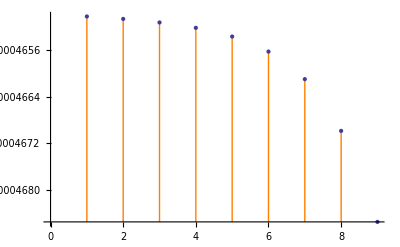

9

```mathematica
Table[GemE[i],{i,1,Iteraties-1}]
ListPlot[Table[GemE[i],{i,1,Iteraties-1}],PlotStyle->Automatic,Filling->GemE[Iteraties-1],FillingStyle->Orange,Mesh->None]
Length[Table[GemE[i],{i,1,Iteraties-1}]]
```

```mathematica
Manipulate[VectorPlot[{Btot[[1]]/.z->a,Btot[[2]]/.z->a},{x,-30,30},{y,-30,30}],{{a,0},-10,10,1}]
```

```mathematica
ContourPlot3D[Btot[[1]]+Btot[[2]]+Btot[[3]]==0,{x,-30,30},{y,-30,30},{z,-30,30}]
```

-Graphics3D-

```mathematica
Output=Show[
Graphics3D[
{Opacity[.3],Table[Sphere[p[n],10],{n,1,Length[positions]}]}],
Graphics3D[Table[Arrow[{p[j]-10*vectors[[j]],p[j]+10*vectors[[j]]}],{j,1,Length[positions]}]],
Graphics3D[{Dashed,Red,Thick,Table[Arrow[{p[j]-10*F[j],(p[j]+10F[j])}],{j,1,Length[positions]}]}],
VectorPlot3D[{Btot[[1]],Btot[[2]],Btot[[3]]},{x,-30,30},{y,-30,30},{z,-30,30}]
,Axes->True,ViewPoint->{2Pi,Pi,3Pi}]
```

-Graphics3D-